# Case Study: Connecting Two Bistable Patches.

```mathematica
eqA = thetaA*zA*(lam12(1-zA) -(lam12 + lam21)zA(1-zA)) - speed*(nuA - 1)(zB - zA);
eqB = thetaB*zB*(iot12(1-zB) - (iot12 + iot21)zB(1-zB)) - speed*(nuB -1)(zA-zB);
```

```mathematica
νA =FullSimplify[ (c (-2-μ (5+2 μ+R0 (-1+ω)+(2+μ) (1+2 μ) ω))+(1+μ) (2+μ (2+(3+2 μ) ω)))/(c (-1+R0) (2+μ (3+2 μ)) (1+μ ω))];
νB=FullSimplify[(-((1+μ) (2+μ ω) (1+2 μ ω))+c (2+μ (3+R0 (-1+ω)+ω (4+5 μ+2 μ (1+μ) ω))))/((-1+c R0) (1+μ) (2+μ ω (3+2 μ ω)))];
θA=2m/(2μ^2 + 3μ  + 2);
θB = 2m/(2(ω*μ)^2 + 3*ω*μ  + 2);
m = 1.5;
```

# Using Free Invasion Fitness’

```mathematica
R0 = 2;
μ = 1;
d = 1;
```

```mathematica
λ12 = -1;
λ21 = -1;
ι12 = -1;
ι21 = -1;
```

```mathematica
FreeRegionPlot[4, 0.5, 3, R0, μ, d, λ12, λ21, ι12, ι21]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

$Aborted

So it would seem that connecting two bistable patches, leads to a bistable outcome. But maybe this depends on invasion fitness magnitude or speed.

## Varying Invasion Fitness Magnitude: Increasing the magnitude of ι21.

```mathematica
λ12 = -1;
λ21 = -1;
ι12 = -1;
ι21 = Table[k*ι12, {k, 1, 10, 4}]
```

{-1,-5,-9}

```mathematica
FreeRegionPlot[4, 0.5, 3, R0, μ, d, λ12, λ21, ι12, ι21[[1]]]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

-Graphics-

```mathematica
FreeRegionPlot[4, 0.5, 3, R0, μ, d, λ12, λ21, ι12, ι21[[2]]]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

-Graphics-

```mathematica
FreeRegionPlot[4, 0.5, 3, R0, μ, d, λ12, λ21, ι12, ι21[[3]]]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

-Graphics-

So it seems that varying the magnitude of invasion fitness over one patch does not alter the behaviour of the coupled system.

## Varying Invasion Fitness Magnitude : Increasing the magnitude of λ21 and ι21 .

```mathematica
λ12 = -1;
λ21 = Table[k*λ12, {k, 1, 10, 4}]
ι12 = -1;
ι21 = Table[k*ι12, {k, 1, 10, 4}]
```

{-1,-5,-9}

{-1,-5,-9}

```mathematica
FreeRegionPlot[4, 0.5, 3, R0, μ, d, λ12, λ21[[2]], ι12, ι21[[2]]]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
FreeRegionPlot[4, 0.5, 3, R0, μ, d, λ12, λ21[[3]], ι12, ι21[[3]]]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

This approach doesn’t lead to very interesting results. Bistability is always from these parameter combinations. We will make use of the nullcline plots to try and find cases where the behaviour is not so straightforward. If we push the parameter set to a case where there is more than one coexistence point we might loose the Bistable behaviour in the coupled system, or rather, might fall into cases of triple stability.

## Varying Invasion Fitness Magnitude : Finding Critical Values for the invasion fitness’

```mathematica
Manipulate[FreeNullclines[c, ω, R0, μ, d, λ12, λ21, ι12, ι21], {c, 1/R0 +0.001, 4}, {ω, 0.5, 3}, {λ12, -0.1, -20}, {λ21, -0.1, -20}, {ι12, -0.1, -20}, {ι21, -0.1, -20}]
```

Having very large invasion fitness magnitudes in general forces the system into region with multiple coexistence points! Lets try to do the previous plots with this kind of extreme invasion fitness’

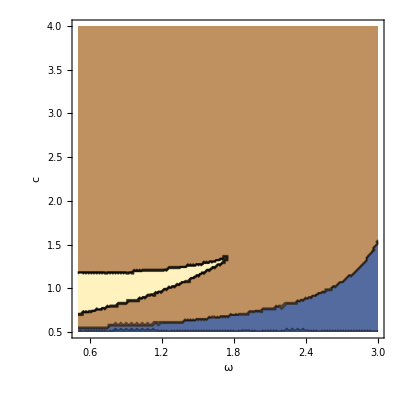

```mathematica
ContourPlot[CoexNumber[c, ω, R0, μ, d, -20, -20, -20, -20], {ω, 0.5,3}, {c, 1/R0, 4}, PlotTheme->"Detailed", FrameLabel->{"ω", "c"}, Contours->10, PlotLegends->{"0", "1"}, PlotTheme->"Detailed", WorkingPrecision->10]
```

```mathematica
Manipulate[FreePhase[c, ω, R0, μ, d, λ12, λ21, ι12, ι21], {c, 1/R0 +0.001, 4}, {ω, 0.5, 3}, {λ12, -0.1, -30}, {λ21, -0.1, -30}, {ι12, -0.1, -30}, {ι21, -0.1, -30}]
```

These parameters lead to 3 coex point but Bistability is preserved.

```mathematica
points=FreeEquilibria[4, 2, R0, μ, d, -20, -20, -20, -20]
StabilityReport[4, 2, R0, μ, d, -20, -20, -20, -20, points]
```

{{zA→1.,zB→1.},{zA→0.801962,zB→0.400459},{zA→0.5,zB→0.5},{zA→0.198038,zB→0.599541},{zA→0.,zB→0.}}

({zA→1.,zB→1.} | True
{zA→0.801962,zB→0.400459} | False
{zA→0.5,zB→0.5} | False
{zA→0.198038,zB→0.599541} | False
{zA→0.,zB→0.} | True)

These parameters lead to 5 coex points and Bistability is lost. We have two stable coexistence points and 3 unstable ones.

```mathematica
points=FreeEquilibria[2.5, 2, R0, μ, d, -30, -30, -25, -30]
StabilityReport[2.5, 2, R0, μ, d, -20, -20, -25, -20, points]
```

{{zA→1.,zB→1.},{zA→0.882611,zB→0.330894},{zA→0.772988,zB→0.106293},{zA→0.525678,zB→0.436569},{zA→0.733948,zB→0.0981587},{zA→0.0876119,zB→0.546399},{zA→0.,zB→0.}}

({zA→1.,zB→1.} | True
{zA→0.882611,zB→0.330894} | False
{zA→0.772988,zB→0.106293} | True
{zA→0.525678,zB→0.436569} | False
{zA→0.733948,zB→0.0981587} | True
{zA→0.0876119,zB→0.546399} | False
{zA→0.,zB→0.} | True)

Finally, these parameters lead to 7 coexistence points and bistability is also lost. We have 4 stable coexistence equilibria and 5 unstable ones.

```mathematica
points=FreeEquilibria[1.5, 2, R0, μ, d, -30, -30, -30, -30]
StabilityReport[1.5, 2, R0, μ, d, -30, -30, -30, -30, points]
```

{{zA→1.,zB→1.},{zA→0.914569,zB→0.356333},{zA→0.360964,zB→0.913683},{zA→0.867053,zB→0.137863},{zA→0.5,zB→0.5},{zA→0.132947,zB→0.862137},{zA→0.639036,zB→0.0863173},{zA→0.0854314,zB→0.643667},{zA→0.,zB→0.}}

({zA→1.,zB→1.} | True
{zA→0.914569,zB→0.356333} | False
{zA→0.360964,zB→0.913683} | False
{zA→0.867053,zB→0.137863} | True
{zA→0.5,zB→0.5} | False
{zA→0.132947,zB→0.862137} | True
{zA→0.639036,zB→0.0863173} | False
{zA→0.0854314,zB→0.643667} | False
{zA→0.,zB→0.} | True)

We can simulate this system to confirm the results:

```mathematica
sols = Table[FreeSolution[1.17, 1.4, R0, μ, d, -20, -20, -20, -20, a, b], {a, 0, 1, 0.1}, {b, 0, 1, 0.1}];
Manipulate[Plot[{zA[t]/.sols[[a]][[ b]], zB[t]/.sols[[a, b]]}, {t, 0, 10}, PlotRange->{-0.01, 1}, PlotTheme->"Detailed", FrameLabel->{"τ", "z"}, PlotLegends->{"",""}, ImageSize->800]
,{a, 1, 10, 1}, {b, 1, 10, 1}]
```

This shows that multi stability between exclusion and coexistence equilibria is possible in the coupled system. Nevertheless, in order to find these scenarios we we’re forced to take very large invasion fitness magnitudes which, in principle, should not arise biologically, as strain dissimilarity is taken to be small enough. Because of this, it seems more reasonable to conduct this analysis with the bottom up approach to the invasion fitness’. 

The nature of these results is also tied with the magnitude difference between the patch specific parameters and the strain specific parameters. These cases that lead to greater coexistence numbers required very different magnitudes for the invasion fitness and the patch specific parameter ratios. For example, in the last parameter set, the invasion fitness magnitude considered is 12 times the R0 ratio between patches and 30 times the μ ratio between patches. This suggests we are pushing the system into a really extreme cases and so it is natural that it does not behave in a predictable way.

```mathematica
FreeRegionPlot[4, 0.5, 3, R0, μ, d, -20, -20, -20, -20]
```

-Graphics-

We can verify the these predicitons:

```mathematica
c = 1.15;
ω = 1.4;
sols = Table[FreeSolution[c, ω, R0, μ, d, -20, -20, -20, -20, a, b], {a, 0, 1, 0.1}, {b, 0, 1, 0.1}];
points20=FreeEquilibria[c, ω, R0, μ, d, -20, -20, -20, -20]
stability = StabilityReport[c, ω, R0, μ, d, -20, -20, -20, -20, points20]
stableEq = Table[If[stability[[1, i]][[2]] == True, stability[[1, i]][[1]], {zA->-100,zB -> -100}], {i, 1, Length[stability[[1]]], 1}];
unstableEq = Table[If[stability[[1, i]][[2]] == False, stability[[1, i]][[1]], {zA-> -100, zB-> -100}], {i, 1, Length[stability[[1]]], 1}];
Manipulate[Plot[{zA[t]/.sols[[a]][[ b]], zB[t]/.sols[[a, b]]}, {t, 0, 10}, PlotRange->{-0.01, 1}, PlotTheme->"Detailed", FrameLabel->{"τ", "z"}, PlotLegends->{"",""}, ImageSize->800]
,{a, 1, 10, 1}, {b, 1, 10, 1}]
```

{{zA→1.,zB→1.},{zA→0.882707,zB→0.314103},{zA→0.834559,zB→0.17169},{zA→0.319589,zB→0.882553},{zA→0.5,zB→0.5},{zA→0.680411,zB→0.117447},{zA→0.165441,zB→0.82831},{zA→0.117293,zB→0.685897},{zA→0.,zB→0.}}

({zA→1.,zB→1.} | True
{zA→0.882707,zB→0.314103} | False
{zA→0.834559,zB→0.17169} | True
{zA→0.319589,zB→0.882553} | False
{zA→0.5,zB→0.5} | False
{zA→0.680411,zB→0.117447} | False
{zA→0.165441,zB→0.82831} | True
{zA→0.117293,zB→0.685897} | False
{zA→0.,zB→0.} | True)

# Using the bottom-up approach to the invasion fitness’

We need to select an Alpha matrix that leads to the connection of two bistable patches.

```mathematica
Clear[λ12, λ21]
```

```mathematica
μ = 1;
```

```mathematica
Subscript[θ, 5][ R0_, μ_] := (R0*m)/(2*m)*μ*(1 - 1/R0);
λ12[R0_, μ_, Alpha_] := Subscript[θ, 5][R0, μ]*(μ(Alpha[[2]][[1]] - Alpha[[1]][[2]]) + Alpha[[2]][[1]] - Alpha[[2]][[2]]);
λ21[R0_, μ_, Alpha_] := Subscript[θ, 5][R0, μ]*(μ(Alpha[[1]][[2]] - Alpha[[2]][[1]]) + Alpha[[1]][[2]] - Alpha[[1]][[1]]);
```

```mathematica
Alpha = -15*{{-1.9, .3},
		{.6, -0.9}};
Alpha // MatrixForm
```

(28.5 | -4.5
-9. | 13.5)

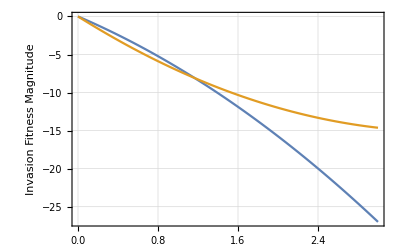

```mathematica
Plot[{λ12[1.5, μ, Alpha], λ21[1.5, μ, Alpha]}, {μ, 0, 3}, PlotLegends->{"", ""}, FrameLabel->{"", "Invasion Fitness Magnitude"}, PlotTheme->"Detailed"]
```

```mathematica
Manipulate[Phase[c, ω, R0, μ, d, Alpha], {c, 1/R0, 4}, {ω, 0, 5}]
```

```mathematica
OutcomePlot[4, 0.5, 1.5, R0, μ, d, Alpha]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
coexP = RegionPlot[{CoexNumber[c, ω, R0, μ, d, Alpha] > 1}, {ω, 0.5, 1.5}, {c, 1/R0 +0.0001, 4},PlotLegends->{"More than 1 Coex point"} , PlotTheme->"Detailed", FrameLabel->{"ω", "c"}, PerformanceGoal->"Speed"]
```

$Aborted

```mathematica
CoexNumber[3,2, R0, μ, d, Alpha]
```

1

# Pointwise Analysis

```mathematica
d = 1;
```

```mathematica
R0 = 2;
μ = 1;
```

## Patches are equal in every regard:

```mathematica
c =1;
ω = 1;
```

```mathematica
λ12 = -1;
λ21 = -1;
ι12 = -1;
ι21 = -1;
```

```mathematica
points=FreeEquilibria[c, ω, R0, μ, d, λ12, λ21, ι12, ι21]
StabilityReport[c, ω, R0, μ, d, λ12, λ21, ι12, ι21, points]
```

{{zA→1.,zB→1.},{zA→0.5,zB→0.5},{zA→0.,zB→0.}}

({zA→1.,zB→1.} | True
{zA→0.5,zB→0.5} | False
{zA→0.,zB→0.} | True)

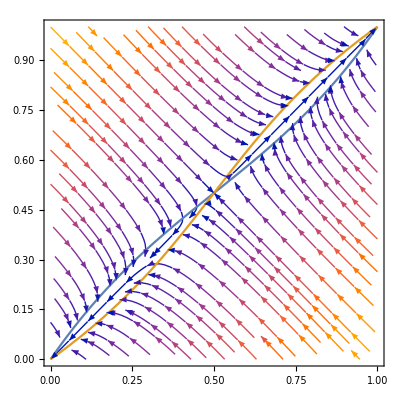

```mathematica
FreePhase[c, ω, R0, μ, d, λ12, λ21, ι12, ι21]
```

>>>>>> Everything is as expected. If the lambdas are equal (1/2, 1/2) is always a coex point. This case where patches are equal in every regard is just like the uncoupled behaviour: two exactly equal patches is like one big patch.

## Introducing variation in μ (increasing or decreasing ω)

Fixing μA = 1 and varying  ω allows us to differentiate patch A from patch B in the axis of single to double infection ratios.

```mathematica
Clear[ω]
```

```mathematica
Manipulate[StabilityReport[c, ω, R0, μ, d, λ12, λ21, ι12, ι21,FreeEquilibria[c, ω, R0, μ, d, λ12, λ21, ι12, ι21]], {ω, 0.5, 300} ]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Det::matsq: Argument {{-1.13228+0.428571 λ12,1.13228},{{0.895989,0.895989,0.895989},{-1.64599,-1.64599,-1.64599}}} at position 1 is not a non-empty square matrix.

Tr::rect: Nonrectangular tensor encountered.

```mathematica
Manipulate[FreePhase[c, ω, R0, μ, d, λ12, λ21, ι12, ι21], {ω, 0, 10}]
```

Increasing ω doesn't change the equilibria so the qualitative behaviour of this system is maintained .

## Changing R0B (variation in c)

```mathematica
ω = 1;
Clear[c]
```

```mathematica
Manipulate[StabilityReport[c, ω, R0, μ, d, λ12, λ21, ι12, ι21,FreeEquilibria[c, ω, R0, μ, d, λ12, λ21, ι12, ι21]], {c, 1/R0 + 0.001, 4} ]
```

```mathematica
Manipulate[FreePhase[c, ω, R0, μ, d, λ12, λ21, ι12, ι21], {c, 1/R0 + 0.001, 4}]
```

## Changing R0B and μB simultaneously:

```mathematica
Manipulate[FreePhase[c, ω, R0, μ, d, λ12, λ21, ι12, ι21], {c, 1/R0 + 0.001, 4}, {ω, 0.5, 3}]
```

### This means that changes in Patch specific parameters doesn’t affect the outcome of the coupled system. This makes sense: If both patches select strains in a bistable manner, it doesn’t matter which patch is more suitable for infection or not, once they are connected they will still select strains in a bistable manner. The threshold for selection also isn’t affected because they have exactly the same coexistence equilibrium (0.5, 0.5). If we change λ12, λ21, ι12, ι21 to some other value but in a way that they remain equal we will still see the same behaviour! Along these directions where λ12 = ι12 = λ21 = ι21 we will always see this qualitative type of behaviour. (Unless we push the system to some more extreme values of fitness. Then we get more coexistence points and you can have multistability)

```mathematica
Manipulate[FreePhase[c, ω, R0, μ, d, -a, -a, -a, -a], {c, 1/R0 + 0.001, 4}, {ω, 0.5, 3}, {a, 0, 20}]
```

## Changing fitness in A:

### Keeping μ and R0 equal

```mathematica
c = 1;
ω = 1;
```

```mathematica
ι12 = -1;
ι21 = -1;
λ12 = -1;
```

```mathematica
Manipulate[StabilityReport[c, ω, R0, μ, d, λ12, λ21, ι12, ι21,FreeEquilibria[c, ω, R0, μ, d, λ12, λ21, ι12, ι21]], {λ21, -0.5, -10} ]
```

```mathematica
Manipulate[FreePhase[c, ω, R0, μ, d, λ12, λ21, ι12, ι21], {λ21, -0.5, -10}]
```

Only changing λ21 moves the coex point but doesn’t alter the behaviour. The nullcline for eqB stays equal but the nullcline for  A moves.

### Changing R0

```mathematica
Manipulate[FreePhase[c, ω, R0, μ, d, λ12, λ21, ι12, ι21], {λ21, -0.5, -10}, {c, 1/R0 + 0.001, 2}]
```

```mathematica
Manipulate[FreePhase[c, ω, R0, μ, d, λ12, λ21, ι12, ι21], {λ21, -0.5, -10}, {c, 1/R0 + 0.001, 2}, {ω, 0.5, 3}]
```

Ultimately, the added change in R0 and μ changes the shape of the nullclines but doesn’t alter qualitative outcome of the system. The change in the treshold for selections does however mean that one strain is more likely than the other to be selected!

### Changing ι21 and c and ω

```mathematica
Manipulate[FreePhase[c, ω, R0, μ, d, λ12, λ21, ι12, ι21], {ι21, -0.5, -10}, {c, 1/R0 + 0.001, 2}, {ω, 0.5, 3}]
```

Has the same kind of behaviour, only the variation happens in the nullcline for B.

### Changing ι21, λ21 and c and ω

```mathematica
Manipulate[FreePhase[c, ω, R0, μ, d, λ12, λ21, ι12, ι21], {λ21, -0.5, -10},{ι21, -0.5, -10}, {c, 1/R0 + 0.001, 2}, {ω, 0.5, 3}]
```

The system is still bistable but notice that the regions of attraction for (1, 1) are much bigger! The more negative λ21 and ι21 are the more likely you are to select strain 1!

### Changing ι21, λ12 and c and ω.

Changing ι21 will make patch B prefer strain 1 and changing λ12 will make patch A prefer strain 2. Now the play of c and ω should be important.

```mathematica
Manipulate[FreePhase[c, ω, R0, μ, d, λ12, λ21, ι12, ι21], {λ12, -0.5, -10},{ι21, -0.5, -10}, {c, 1/R0 + 0.001, 2}, {ω, 0.5, 3}]
```

If patch A has a much stronger fitness preference, then increasing c doesn’t have enough of an effect to alter the size of the regions of attraction.

# A Special System to better understand Bistability

```mathematica
R0 = 2;
μ = 1;
d = 1;
c = 1;
ω = 1;
```

```mathematica
λ12 =-9.51;
λ21 = -1;
ι12 = -1;
ι21 = -9.68;
```

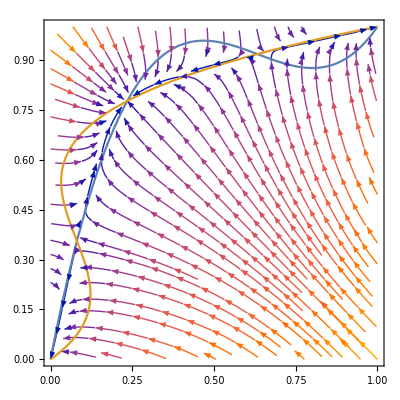

```mathematica
FreePhase[1, 1, R0, μ, d, -9.51, -1, -1, -9.68]
```

```mathematica
R0 = 2;
c = 1;
μ = 1;
ω = 1;
```

```mathematica
points = FreeEquilibria[1, 1, R0, μ, d, -9.68, -1, -1, -9.51];
StabilityReport[1, 1, R0, μ, d, -9.68, -1, -1, -9.51, points]
```

({zA→1.,zB→1.} | True
{zA→0.643992,zB→0.919324} | False
{zA→0.223192,zB→0.765341} | True
{zA→0.0823699,zB→0.367443} | False
{zA→0.,zB→0.} | True)

```mathematica
sols = Table[FreeSolution[1, 1, R0, μ, d, -9.68, -1, -1, -9.51, a, b], {a, 0, 1, 0.1}, {b, 0, 1, 0.1}];
stability = StabilityReport[1, 1, R0, μ, d, -9.68, -1, -1, -9.51, points];
stableEq = Table[If[stability[[1, i]][[2]] == True, stability[[1, i]][[1]], {zA->-100,zB -> -100}], {i, 1, Length[stability[[1]]], 1}];
unstableEq = Table[If[stability[[1, i]][[2]] == False, stability[[1, i]][[1]], {zA-> -100, zB-> -100}], {i, 1, Length[stability[[1]]], 1}];
Manipulate[GraphicsRow[{Plot[{zA[t]/.sols[[a]][[ b]], 1 -zA[t]/.sols[[a, b]]}, {t, 0, 10}, PlotRange->{-0.01, 1}, PlotTheme->"Detailed", FrameLabel->{"τ", "z"}, PlotLegends->{"",""}, ImageSize->500, PlotLabel->"Patch A"], 
Plot[{zB[t]/.sols[[a]][[ b]], 1- zB[t]/.sols[[a, b]]}, {t, 0, 10}, PlotRange->{-0.01, 1.01}, PlotTheme->"Detailed", FrameLabel->{"τ", "z"}, PlotLegends->{"",""}, ImageSize->500, PlotLabel->"Patch B"]}, ImageSize-> 1200

], {a, 1, 10, 1}, {b, 1, 10, 1}]
```

```mathematica
Manipulate[Plot[{zA[t]/.sols[[a]][[ b]], zB[t]/.sols[[a, b]]}, {t, 0, 10}, PlotRange->{-0.01, 1}, PlotTheme->"Detailed", FrameLabel->{"τ", "z"}, PlotLegends->{"",""}, ImageSize->800]
,{a, 1, 10, 1}, {b, 1, 10, 1}]
```

```mathematica
Manipulate[FreePhase[1, 1, R0, μ, d, -9.68, -1, -1, -9.51], {d, 0, 50}]
```

```mathematica
pointsD = FreeEquilibria[1, 1, R0, μ, 5, -9.68, λ21, ι12, -9.51];
StabilityReport[1, 1, R0, μ, 5, -9.68, λ21, ι12, -9.51, pointsD]
```

({zA→1.,zB→1.} | True
{zA→0.454146,zB→0.556769} | False
{zA→0.,zB→0.} | True)

```mathematica
-9.68/(-9.68-1)
```

0.906367